```mathematica
By Le Chen.
Crated on Mon 06 Jun 2022 10:06:53 AM EDT
```

```mathematica
Solve[D[k Log[t] - a t,t]==0,t]
```

{{t→k/a}}

```mathematica
t^k Exp[-a t]/.t->k/a//FullSimplify
```

ⅇ^-k (k/a)^k

```mathematica
Integrate[s Exp[-a s],{s,0,t},Assumptions->a>0]
```

(1-ⅇ^(-a t) (1+a t))/a^2

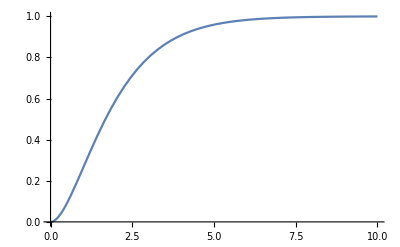

```mathematica
Plot[(1-ⅇ^(-a t) (1+a t))/a^2/.a->1,{t,0,10}]
```

```mathematica
Integrate[s Exp[-a s],{s,0,∞},Assumptions->a>0]
```

1/a^2

```mathematica
Integrate[Exp[-2a u] u^(ρ-1),{u,0,∞}]
```